## Bistable system in BG02

```mathematica
ϵ =1.8*10^(-4);
k=.39;
A=5*10^(-4);
f[x_,t_]:=1/ϵ((x - x^3 )(1+A Cos[2Pi t])+ k Cos[2Pi t]);
```

```mathematica
V[x_,t_]:=-(1/2x^2 - 1/4x^4 + x k Cos[2Pi t]);
```

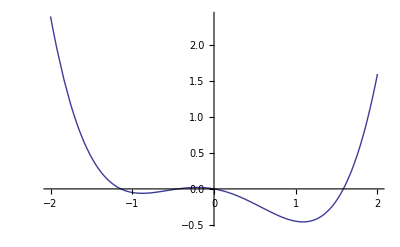

```mathematica
Plot[V[x,0],{x,-2,2}]
```

```mathematica
M=20;
S=NDSolve[{x'[t]==f[x[t],t],x[0]==0},x,{t,0,M},MaxSteps->200000]
```

{{x→InterpolatingFunction[{{0.,20.}},<>]}}

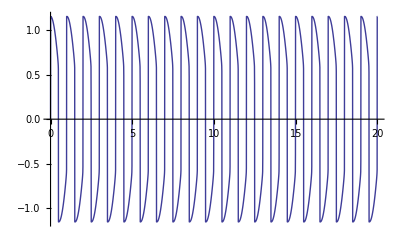

```mathematica
Plot[x[t]/.S,{t,0,M}]
```

## Bistable system in JH Yang et al

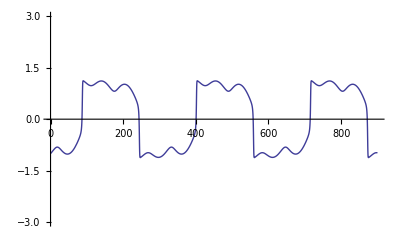

```mathematica
a=1;
b=1;
F=.4;
ω=.06;
θ=.04;
dx[x_,t_]:=.97(a x -  b x^3) + F Sin[ω t]Cos[θ t];
S=NDSolve[{x'[t]==dx[x[t],t],x[0]==-1},x,{t,0,900},MaxSteps->10^6];
Plot[(x[t]/.S),{t,0,900},PlotRange->{-3,3}]
```

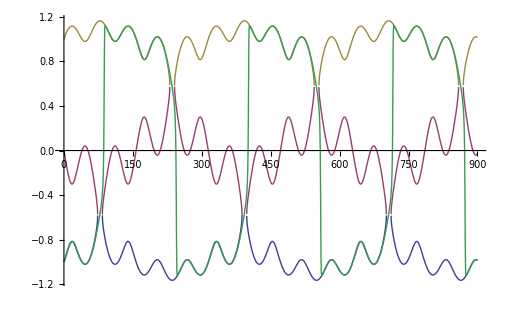

```mathematica
Plot[{Solve[dx[x,d]==0,x][[1]][[1]][[2]],Solve[dx[x,d]==0,x][[2]][[1]][[2]],Solve[dx[x,d]==0,x][[3]][[1]][[2]],x[d]/.S},{d,0,900}]
```

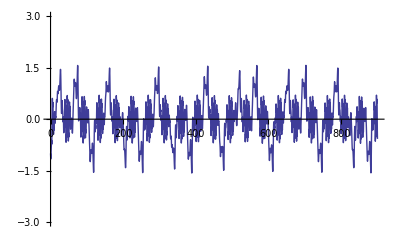

```mathematica
a=1;
b=1;
F=1.81;
ω=1;
θ=.07;
dx[x_,t_]:=.97(a x -  b x^3);
S=NDSolve[{x'[t]==dx[x[t] + F Sin[ω t]Cos[θ t],t],x[0]==-1},x,{t,0,900},MaxSteps->10^6];
Plot[(x[t]/.S),{t,0,900},PlotRange->{-3,3}]
```

## Triple well system in H. Zhang et al

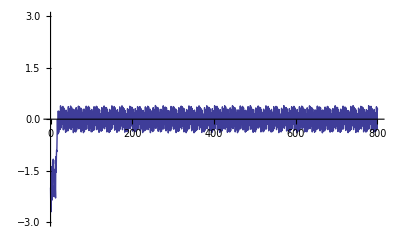

```mathematica
b=.25;
a=0;
c=1;
F=.95;
ω=2.8;
θ=.5;
dx[x_,t_]=-D[x^2(b x^2 - c)^2+a x^2,x];
S=NDSolve[{x'[t]==dx[x[t]+ F Sin[ω t]Cos[θ t],t],x[0]==-2},x,{t,0,800},MaxSteps->10^6];
Plot[(x[t]/.S),{t,0,800},PlotRange->{-3,3}]
```

5.51 Cos[0.5 t] Cos[5.8 t]-0.475 Sin[0.5 t] Sin[5.8 t]

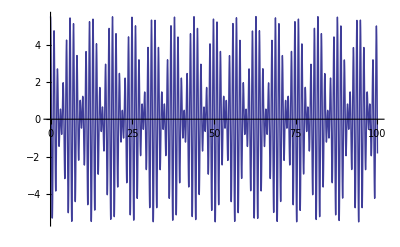

```mathematica
z[t_]=D[F Sin[ω t]Cos[θ t],t]
Plot[z[t],{t,0,100}]
```

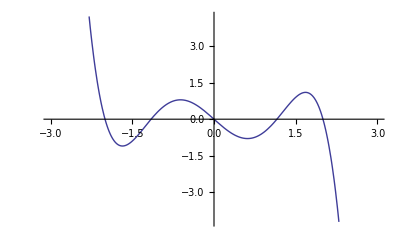

```mathematica
Plot[dx[x,0],{x,-3,3}]
```